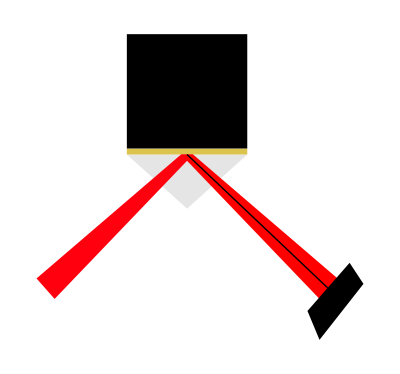

```mathematica
Graphics[{Hue[0.5,0,0.5,0.2],Triangle[{{-0.5,-1},{0,-1.45},{0.5,-1}}],Hue[0.14,0.65,0.86,1],Rectangle[{-0.5,-1},{0.5,-0.95}],Hue[0.99,1.,1.],Polygon[{{-1.1,-2.2},{-1.25,-2.03},{-0.05,-1},{0.05,-1}}],Hue[1,1.,1.],Polygon[{{1.1,-2.2},{1.25,-2.03},{0.05,-1},{-0.05,-1}}],Hue[0.5,0.5,0],Line[{{1.175,-2.115},{0,-1}}],Polygon[{{1.35,-1.9},{1.465,-2.075},{1.1,-2.54},{1,-2.3}}],Rectangle[{-0.5,-0.95},{0.5,0}]}]
```

```mathematica
m=(-2.03+2.2)/(1.25-1.1)
```

1.13333

```mathematica
-m*1.1-2.2
```

-3.44667

```mathematica
camerafront[x_] = m*x-3.44667
```

Set::write: Tag Plus in (-3.44667+1.13333 x)[x_] is Protected.

-3.44667+1.13333 x

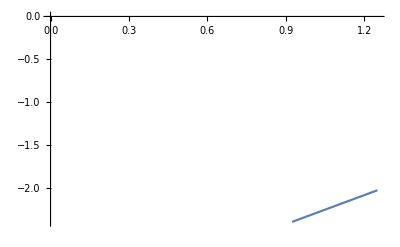

```mathematica
Plot[camerafront,{x,0,1.25},PlotRange->{-2.4,0}]
```

```mathematica
camerafront[2]
```

(-3.44667+1.13333 x)[2]

```mathematica
f1[x_]=m*x-3.4467
```

-3.4467+1.13333 x

```mathematica
f2[x_]=m*x-3.7467
```

-3.7467+1.13333 x

```mathematica
f2[1.475]
```

-2.07503

```mathematica
f1[1.475]
```

-1.77503

```mathematica
f1[0.8]
```

-2.54003

```mathematica
f2[0.8]
```

-2.84003